```mathematica
Clear["Global`*"]
x=5;
y=13.5;
R=8;

(*Sol=Solve[{
x==R(Cos[θ]+Cos[ϕ]),
y==R(Sin[θ]+Sin[ϕ])},{θ,ϕ}];*)


θ={ArcTan[(R x^3+R x y^2-√(4 R^4 x^2 y^2-R^2 x^4 y^2+4 R^4 y^4-2 R^2 x^2 y^4-R^2 y^6))/(2 (R^2 x^2+R^2 y^2)),1/(2 R y)(x^2+y^2-(R^2 x^4)/(R^2 x^2+R^2 y^2)-(R^2 x^2 y^2)/(R^2 x^2+R^2 y^2)+(R x √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))],ArcTan[(R x^3+R x y^2+√(4 R^4 x^2 y^2-R^2 x^4 y^2+4 R^4 y^4-2 R^2 x^2 y^4-R^2 y^6))/(2 (R^2 x^2+R^2 y^2)),1/(2 R y)(x^2+y^2-(R^2 x^4)/(R^2 x^2+R^2 y^2)-(R^2 x^2 y^2)/(R^2 x^2+R^2 y^2)-(R x √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))]};
ϕ={ArcTan[(2 x-(R^2 x^3)/(R^2 x^2+R^2 y^2)-(R^2 x y^2)/(R^2 x^2+R^2 y^2)+(R √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))/(2 R),1/(2 R y)(-x^2+y^2+(R^2 x^4)/(R^2 x^2+R^2 y^2)+(R^2 x^2 y^2)/(R^2 x^2+R^2 y^2)-(R x √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))],ArcTan[(2 x-(R^2 x^3)/(R^2 x^2+R^2 y^2)-(R^2 x y^2)/(R^2 x^2+R^2 y^2)-(R √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))/(2 R),1/(2 R y)(-x^2+y^2+(R^2 x^4)/(R^2 x^2+R^2 y^2)+(R^2 x^2 y^2)/(R^2 x^2+R^2 y^2)+(R x √(-R^2 y^2 (-4 R^2 x^2+x^4-4 R^2 y^2+2 x^2 y^2+y^4)))/(R^2 x^2+R^2 y^2))]};
x1=R Cos[θ];
y1=R Sin[θ];
x2=R Cos[ϕ];
y2=R Sin[ϕ];
Graphics[{Disk[],
(*
Line[{{0,0},{x1[[1]],y1[[1]]}}],
Line[{{x1[[1]],y1[[1]]},{x2[[1]]+x1[[1]],y2[[1]]+y1[[1]]}}],

Line[{{0,0},{x1[[2]],y1[[2]]}}],
Line[{{x1[[2]],y1[[2]]},{x2[[2]]+x1[[2]],y2[[2]]+y1[[2]]}}],PlotRange->{{0,16},{0,16}},*)
Dynamic[MousePosition["Graphics"]]
}]
```

-Graphics-

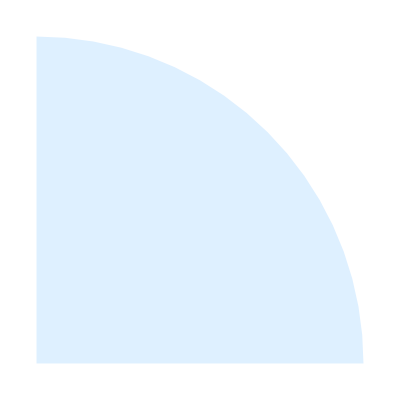

```mathematica
Graphics[{LightBlue,Disk[{0,0},1,{0,Pi/2}],ImageSize->400}]
point=Dynamic[MousePosition["Graphics"]*16];
point
```